# Grammar-based genetic programming

## Grammar definition and parsing

```mathematica
grammar = {
<|"From"->"cond","To"->{Term["logicOp"],NonTerm["cond"],NonTerm["cond"]},
"Value"->Term["logicOp"]["Value"][NonTerm["cond"]["Value"],NonTerm["cond"]["Value"]]|>,
<|"From"->"cond","To"->{Term["not"],NonTerm["cond"]},
"Value"->Not[NonTerm["cond"]["Value"]]|>,
<|"From"->"cond","To"->{Term["numOp"],NonTerm["numQuant"],NonTerm["numQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["numQuant"]["Value"],NonTerm["numQuant"]["Value"]]|>,
<|"From"->"numQuant","To"->{Term["factor"],NonTerm["expression"]},
"Value"->Times[Term["factor"]["Value"],NonTerm["expression"]["Value"]]|>,
<|"From"->"numQuant","To"->{NonTerm["expression"]},
"Value"->NonTerm["expression"]["Value"]|>,
<|"From"->"expression","To"->{Term["techInd"],Term["observable"],Term["lag"]},
"Value"->Term["techInd"]["Value"][Term["observable"]["Value"],Term["lag"]["Value"]]|>,
<|"From"->"expression","To"->{Term["lag"],Term["observable"]},
"Value"->Prev[Term["observable"]["Value"],Term["lag"]["Value"]]|>,
<|"From"->"expression","To"->{Term["observable"]},
"Value"->Term["observable"]["Value"]|>
};
```

```mathematica
GetComponents[expr_/;Depth[expr]<3]:={expr};
GetComponents[expr_/;Depth[expr]==3]:=Prepend[Level[expr,{1}],Head[expr]];
ExprFromComponents[components_ /;Length[components]≤1]:=First[components];
ExprFromComponents[components_ /;Length[components]>1]:=Block[{head,rest},
{head,rest} = {First[components],Rest[components]};
Apply[head,rest]
];

Synthesize[exprComponents_,synthValues_]:=Block[{positions,lastPos,tmpSynthValues = synthValues,tmpExprComponents = exprComponents},
Do[
positions = Position[tmpSynthValues[[All,1]],tmpExprComponents[[i]]];
If[positions≠ {},
lastPos = First@Last@positions;
tmpExprComponents[[i]] = Replace[tmpExprComponents[[i]],Part[tmpSynthValues,lastPos]];
tmpSynthValues = Delete[tmpSynthValues,lastPos];
];
,{i,1,Length[tmpExprComponents]}
];
ExprFromComponents@tmpExprComponents
];

MatchPositions[expr_,synthesizations_]:=Block[{pos,newSynth,recursive},
pos = FirstPosition[synthesizations,First[expr]];
If[pos =!=Missing["NotFound"],
newSynth = ReplacePart[synthesizations,First[pos]->Found],
newSynth = synthesizations;
pos = {};
];
recursive = If[Rest[expr]≠{},MatchPositions[Rest[expr],newSynth],{}];
Transpose@{Flatten@Join[pos,recursive]}
];
```

```mathematica
GetValue[treeSymbol_,grammar_]:=ReplaceAll[treeSymbol,NonTerm[_,rule_]:>grammar[[rule]]["Value"]];
SynthesizeNonTerm[treeSymbol_,grammar_,synthesizations_]:=Block[{val,eval,matchPos,newSynth,newSynthLabel},
val = GetValue[treeSymbol,grammar];
matchPos = MatchPositions[GetComponents[val],synthesizations[[All,1]]];
eval = Synthesize[GetComponents[val],Extract[synthesizations,matchPos]];
newSynth = Delete[synthesizations,matchPos];
newSynthLabel = ReplaceAll[treeSymbol,NonTerm[x_,_]:>NonTerm[x]["Value"]];

Prepend[newSynth,newSynthLabel->eval]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]==2,
Prepend[synthesizations, ReplaceAll[treeSymbol,Term[termName_,value_]:>(Term[termName]["Value"]->value)]],
synthesizations
]
];
```

```mathematica
SynthesizeTree[graph_,labels_,grammar_]:=Block[{depthFirstScan,labeledDFS,symbolType,synthesized},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[s];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,grammar,synthesized]];
,
{s,labeledDFS}
];

ToExpression@ToString@Return[synthesized[[1,-1]]];
];
```

```mathematica
edgeList1 = {1->2,1->3,1->4,3->5,3->6,3->7,6->8,8->9,7->10,10->11,10->12,4->13,4->14,4->15,14->16,16->17,15->18,18->19};
labels1 = {1->NonTerm["cond",1],2->Term["logicOp","And"],3->NonTerm["cond",3],4->NonTerm["cond",3],5->Term["numOp","Greater"] ,6->NonTerm["numQuant",5] ,7->NonTerm["numQuant",5] ,8->NonTerm["expression",8] ,9->Term["observable","High"] ,10->NonTerm["expression",7] ,11->Term["lag","3"] ,12->Term["observable","Low"] ,13->Term["numOp","Less"] ,14->NonTerm["numQuant",5] ,15->NonTerm["numQuant",5] ,16->NonTerm["expression",8] ,17->Term["observable","Open"] ,18-> NonTerm["expression",8],19-> Term["observable","Close"]};
```

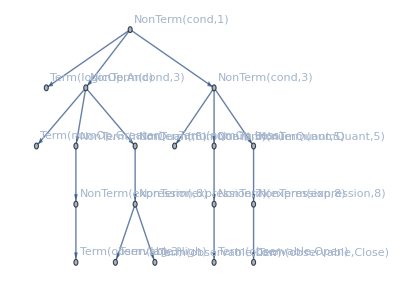

```mathematica
g1 = Graph[edgeList1,VertexLabels->labels1]
```

```mathematica
SynthesizeTree[g1,labels1,grammar] // FullForm
```

And[Greater[High,Prev[Low,3]],Less[Open,Close]]

```mathematica
edgeList2 = {1->2,1->3,1->4,3->5,3->6,3->7,6->8,6->9,9->10,9->11,9->12,7->13,13->14,13->15,13->16,4->17,4->18,4->19,18->20,20->21,20->22,19->23,23->24};
labels2 = {1->NonTerm["cond",1],2->Term["logicOp","Or"],3->NonTerm["cond",3],4->NonTerm["cond",3],5-> Term["numOp","Less"],6->NonTerm["numQuant",4] ,7-> NonTerm["numQuant",5],8->Term["factor",1.05] ,9->NonTerm["expression",6] ,10-> Term["techInd","SMA"],11-> Term["observable","Close"],12->Term["lag",20] ,13->NonTerm["expression",6] ,14->Term["techInd","SMA"] ,15->Term["observable","Close"] ,16->Term["lag",40] ,17->Term["numOp","Less"] ,18->NonTerm["numQuant",5] ,19->NonTerm["numQuant",5] ,20->NonTerm["expression",7],21->Term["lag",2],22->Term["observable","Close"],23->NonTerm["expression",8],24->Term["observable","High"]};
```

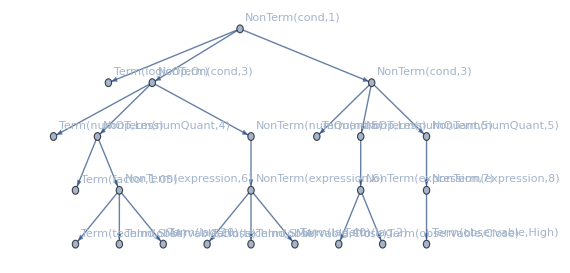

```mathematica
g2 = Graph[edgeList2,VertexLabels->labels2]
```

```mathematica
SynthesizeTree[g2,labels2,grammar]// FullForm
```

Or[Less[Times[1.05,SMA[Close,20]],SMA[Close,40]],Less[Prev[Close,2],High]]